Plot::plln: Limiting value 5 + Mmax in {x, 0, Mmax + 5} is not a machine-sized real number.

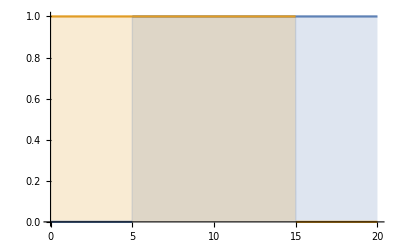

```mathematica
Plot[{HeavisideTheta[x-Mmin],1-HeavisideTheta[x-Mmax]},{x,0,Mmax+5},Filling->Bottom]/.{Mmin->5,Mmax->15}
```

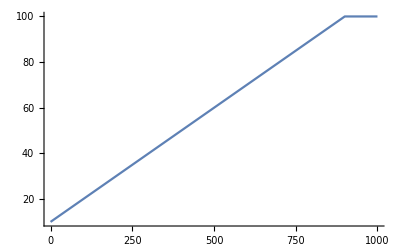

```mathematica
MetapopDyn[Mmin_,Mmax_,Bc_,Mi_,T_] :=

NDSolve[{
Mc'[t] ==HeavisideTheta[Mc[t]-Mmin]*(-Bc + (1-HeavisideTheta[Mc[t]-Mmax])*Mi),
Mc[0]==10},{Mc},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{Mmin=5,Mmax=100,Bc=1.9,Mi=2,T=1000},
Traj=Evaluate[{Mc[t]}/.MetapopDyn[Mmin,Mmax,Bc,Mi,T] ];
Plot[Traj,{t,0,T},PlotRange->{0,All}]
]
```

```mathematica
T = 1000;
StepSize =0.05;
Iterations = 10;
IP[M0_,Mmin_,Mmax_,Bc_,MiBar_,MiSigma_] := ItoProcess[
ⅆMc[t]==HeavisideTheta[Mc[t]-Mmin]*(-Bc*ⅆt+(1-HeavisideTheta[Mc[t]-Mmax])*(MiBar*ⅆt + MiSigma*ⅆw[t])),
Mc[t],{Mc,M0},t,w\[Distributed]WienerProcess[]];
stochsol[M0_,Mmin_,Mmax_,Bc_,MiBar_,MiSigma_] :=
RandomFunction[IP[M0,Mmin,Mmax,Bc,MiBar,MiSigma],{0,T,StepSize},Iterations,Method-> "KloedenPlatenSchurz"];

With[{M0=10,Mmin=5,Mmax=100,Bc=2,MiBar=2.1,MiSigma=1},
TD = stochsol[M0,Mmin,Mmax,Bc,MiBar,MiSigma]["PathComponents"];
ListLinePlot[stochsol[M0,Mmin,Mmax,Bc,MiBar,MiSigma],PlotRange->All,Frame->True,PlotStyle->Thickness[0.002]]
]
```

-Graphics-

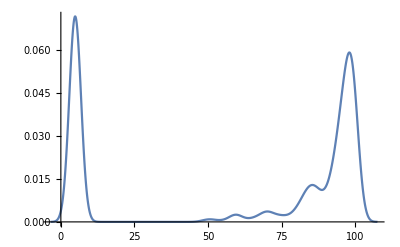

```mathematica
SmoothHistogram[Flatten[TD[[1]][[2]][[1]][[All,IntegerPart[T/StepSize-1000];;IntegerPart[T/StepSize]]],1],2,"PDF",PlotRange->All]
```

```mathematica
Remove["Global`*"]
T = 500;
Iterations = 1;
IP[M0_,Mmin_,Mmax_,Bc_,MiBar_,MiSigma_,xbar_,sigma_,x0_] := ItoProcess[
{ⅆMc[t]==HeavisideTheta[Mc[t]-Mmin]*(-Bc*ⅆt+(1-HeavisideTheta[Mc[t]-Mmax])*(MiBar*ⅆt + MiSigma*ⅆwM[t])),
ⅆxb[t]==Mc[t]/(Mc[t] + 1)*xb[t]*ⅆt+(1-Mc[t]/(Mc[t] + 1))*(xbar*ⅆt + sigma*ⅆwX[t]) - xb[t]*ⅆt},
{Mc[t],xb[t]},{{Mc,xb},{M0,x0}},t,{wM\[Distributed]WienerProcess[],wX\[Distributed]WienerProcess[]}];
stochsol[M0_,Mmin_,Mmax_,Bc_,MiBar_,MiSigma_,xbar_,sigma_,x0_] :=
RandomFunction[IP[M0,Mmin,Mmax,Bc,MiBar,MiSigma,xbar,sigma,x0],{0,T,0.05},Iterations,Method-> "KloedenPlatenSchurz"]
```

```mathematica
nprey = 12;
EX = {-15.5,-17.5,-15.6,-15.5,-14.3,-15.4,-16.0,-17.0,-15.8,-13.3,-17.5,-16.2};
VarX= {1.00,0.81,0.49,0.81,0.81,0.81,0.25,1.21,0.64,1.21,1.96,1.00};
a= {1,1,1,1,1,100,1,1,1,1,1,1};
a0 = Total[a];
Ep = N[a/a0];
Varp = N[Table[(a[[i]]*(a0-a[[i]]))/(a0^2*(a0+1)),{i,1,nprey}]];
Covp =  N[Table[(-a[[i]]*a[[j]])/(a0^2*(a0+1))Boole[i ≠ j],{i,1,nprey},{j,1,nprey}]];
With[{
M0=75,
Mmin=50,
Mmax=100,
Bc=2,
MiBar=2.1,
MiSigma=1,
xbar=N[∑_(i=1)^nprey a[[i]]/a0*EX[[i]]],
sigma = Sqrt[ N[Sum[Varp[[i]]*VarX[[i]] + Ep[[i]]^2*VarX[[i]] + EX[[i]]^2*Varp[[i]] + Sum[Covp[[i]][[j]]*EX[[i]]*EX[[j]]Boole[i ≠ j],{j,1,nprey}],{i,1,nprey}]]],
x0=-15.8},
TD = stochsol[M0,Mmin,Mmax,Bc,MiBar,MiSigma,xbar,sigma,x0]]["PathComponents"];
(*ListLinePlot[stochsol[M0,Mmin,Mmax,Bc,MiBar,MiSigma,xbar,sigma,x0],Frame->True]]*)
```

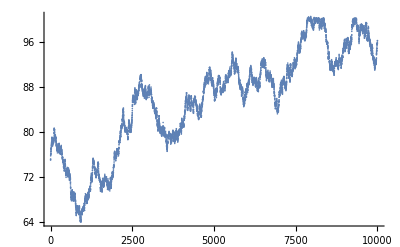

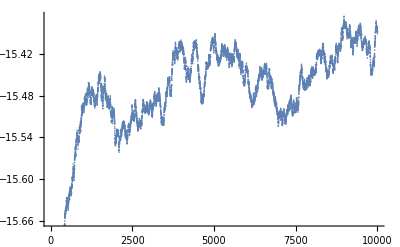

```mathematica
ListPlot[TD[[2]][[1]][[1,All]][[All,1]]]
ListPlot[TD[[2]][[1]][[1,All]][[All,2]]]
```

```mathematica
Remove["Global`*"]
T = 500;
Iterations = 1;
IP[M0_,Mmin_,Mmax_,Bc_,MiBar_,MiSigma_,xbar_,sigma_,x0_] := ItoProcess[
{ⅆMi[t] ==MiBar*ⅆt -( MiBar*ⅆt + MiSigma*ⅆwMi[t]),
ⅆMc[t]==HeavisideTheta[Mc[t]-Mmin]*(-Bc*ⅆt+(1-HeavisideTheta[Mc[t]-Mmax])*Mi[t]),
ⅆxb[t]==Mc[t]/(Mc[t] + 1)*xb[t]*ⅆt+(1-Mc[t]/(Mc[t] + 1))*(xbar*ⅆt + sigma*ⅆwX[t]) - xb[t]*ⅆt},
{Mi[t],Mc[t],xb[t]},{{Mi,Mc,xb},{2,M0,x0}},t,{wMi\[Distributed]WienerProcess[],wX\[Distributed]WienerProcess[]}];
stochsol[M0_,Mmin_,Mmax_,Bc_,MiBar_,MiSigma_,xbar_,sigma_,x0_] :=
RandomFunction[IP[M0,Mmin,Mmax,Bc,MiBar,MiSigma,xbar,sigma,x0],{0,T,0.05},Iterations,Method-> "KloedenPlatenSchurz"]
```

```mathematica
nprey = 12;
EX = {-15.5,-17.5,-15.6,-15.5,-14.3,-15.4,-16.0,-17.0,-15.8,-13.3,-17.5,-16.2};
VarX= {1.00,0.81,0.49,0.81,0.81,0.81,0.25,1.21,0.64,1.21,1.96,1.00};
a= {1,1,1,1,1,100,1,1,1,1,1,1};
a0 = Total[a];
Ep = N[a/a0];
Varp = N[Table[(a[[i]]*(a0-a[[i]]))/(a0^2*(a0+1)),{i,1,nprey}]];
Covp =  N[Table[(-a[[i]]*a[[j]])/(a0^2*(a0+1))Boole[i ≠ j],{i,1,nprey},{j,1,nprey}]];
With[{
M0=75,
Mmin=50,
Mmax=100,
Bc=2,
MiBar=2.1,
MiSigma=1,
xbar=N[∑_(i=1)^nprey a[[i]]/a0*EX[[i]]],
sigma = Sqrt[ N[Sum[Varp[[i]]*VarX[[i]] + Ep[[i]]^2*VarX[[i]] + EX[[i]]^2*Varp[[i]] + Sum[Covp[[i]][[j]]*EX[[i]]*EX[[j]]Boole[i ≠ j],{j,1,nprey}],{i,1,nprey}]]],
x0=-15.8},
TD = stochsol[M0,Mmin,Mmax,Bc,MiBar,MiSigma,xbar,sigma,x0]]["PathComponents"];
(*ListLinePlot[stochsol[M0,Mmin,Mmax,Bc,MiBar,MiSigma,xbar,sigma,x0],Frame->True]]*)
```

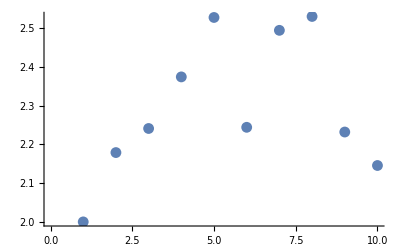

```mathematica
ListPlot[TD[[2]][[1]][[1,All]][[1;;10,1]]]
```

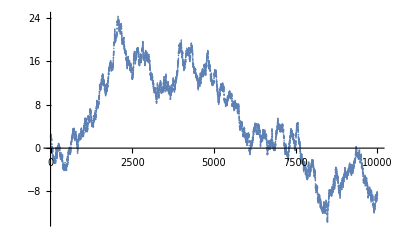

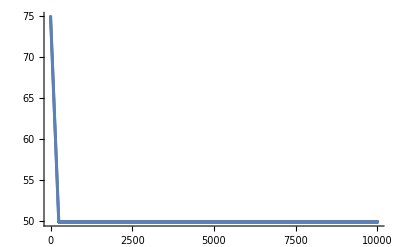

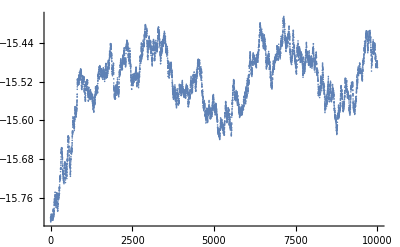

```mathematica
ListPlot[TD[[2]][[1]][[1,All]][[All,1]]]
ListPlot[TD[[2]][[1]][[1,All]][[All,2]]]
ListPlot[TD[[2]][[1]][[1,All]][[All,3]]]
```

```mathematica
DSolve[{x'[t]==-(1-f)*x[t]+(1-f)*mu[t]},{x[t]},t]
```

{{x[t]→ⅇ^((-1+f) t) C[1]+ⅇ^((-1+f) t) ∫_1^t ⅇ^(-(-1+f) K[1]) (mu[K[1]]-f mu[K[1]])ⅆK[1]}}

```mathematica
mut = A + B*Sin[a*t];
dmut = D[mut,t]
```

a B Cos[a t]

```mathematica
DSolve[{x'[t]==-(1-f)*x[t]+(1-f)*mu[t],mu'[t]==a*B*Cos[a*t]},{x[t],mu[t]},t]
```

{{mu[t]→C[1]+B Sin[a t],x[t]→(1-ⅇ^((-1+f) t)) C[1]+ⅇ^((-1+f) t) C[2]+B (1-ⅇ^((-1+f) t)) Sin[a t]+(B ⅇ^((-1+f) t-f t) (a ⅇ^t (-1+f) Cos[a t]+(a^2 (-ⅇ^t+ⅇ^(f t))+ⅇ^(f t) (-1+f)^2) Sin[a t]))/(a^2+(-1+f)^2)}}

```mathematica
FullSimplify[DSolve[{x'[t]==-(1-f)*x[t]+(1-f)*( A + B*Sin[a*t])},{x[t]},t]]
```

{{x[t]→(ⅇ^-t ((a^2+(-1+f)^2) (A ⅇ^t+ⅇ^(f t) C[1])+B ⅇ^t (-1+f) (a Cos[a t]+(-1+f) Sin[a t])))/(a^2+(-1+f)^2)}}

```mathematica
Expand[(-(1-f)*xc*dt +(1-f)*(mu*dt+sig*dw))^2]
```

dt^2 mu^2-2 dt^2 f mu^2+dt^2 f^2 mu^2+2 dt dw mu sig-4 dt dw f mu sig+2 dt dw f^2 mu sig+dw^2 sig^2-2 dw^2 f sig^2+dw^2 f^2 sig^2-2 dt^2 mu xc+4 dt^2 f mu xc-2 dt^2 f^2 mu xc-2 dt dw sig xc+4 dt dw f sig xc-2 dt dw f^2 sig xc+dt^2 xc^2-2 dt^2 f xc^2+dt^2 f^2 xc^2

```mathematica
Expand[(-(1-f)*xc*dt +(1-f)*(mu*dt))^2]
```

dt^2 mu^2-2 dt^2 f mu^2+dt^2 f^2 mu^2-2 dt^2 mu xc+4 dt^2 f mu xc-2 dt^2 f^2 mu xc+dt^2 xc^2-2 dt^2 f xc^2+dt^2 f^2 xc^2

```mathematica
DSolve[x'[t] == sig[t]^2-2*f*sig[t]^2+f^2*sig[t]^2,x[t],t]
```

{{x[t]→C[1]+∫_1^t (sig[K[1]]^2-2 f sig[K[1]]^2+f^2 sig[K[1]]^2)ⅆK[1]}}

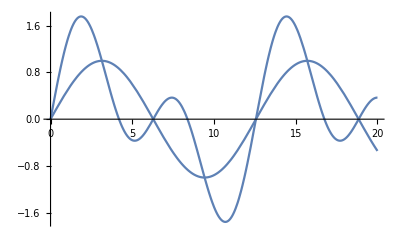

```mathematica
Plot[{Sin[w*t],Sin[w*t] + Sin[2*w*t]}/.w->0.5,{t,0,20}]
```